## ϕ Visibility

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
series=(10#1+#2)&@@@Partition[RealDigits[GoldenRatio,10,20001][[1,2;;]],2];
```

## SDL Complexity

```mathematica
<<sdl.mx
```

```mathematica
result=sdl[series]
```

{{0.136652,0.964583}}

## Visibility

```mathematica
<<visibility.mx
```

```mathematica
links=naturalVisibilityLinks[series];
```

```mathematica
natGraph=Graph[links, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
AppendTo[result,VertexDegree[natGraph]//Mean//N]
```

```mathematica
count=VertexDegree[natGraph]//Counts
```

<|2→2261,9→315,3→2117,5→989,10→263,18→50,6→670,4→1498,12→141,8→371,25→18,19→30,20→25,27→8,7→503,14→110,11→180,16→62,17→51,13→131,15→74,23→21,28→7,30→4,38→1,24→14,22→21,26→6,21→23,32→5,33→5,39→3,42→1,41→1,35→3,52→1,37→2,29→6,31→4,40→1,36→2,34→1|>

```mathematica
If[count[1]<3,count[1]=.];
```

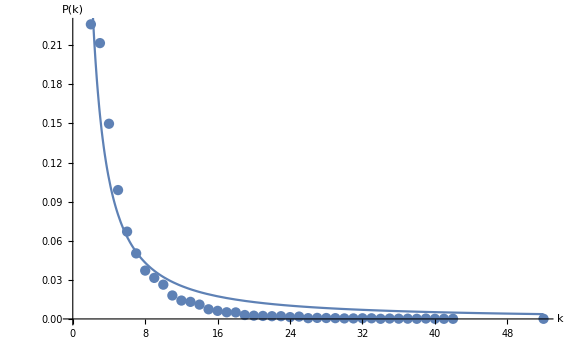
{{{0.664569,0.123812},{1.31484,0.15496}},-Graphics-}

```mathematica
m=plotModel[count,10000]
```

```mathematica
AppendTo[result,m[[1]]]
```

{{0.136652,0.964583},{{0.664569,0.123812},{1.31484,0.15496}}}

## Horizontal Visibility

```mathematica
horlinks=horizontalVisibilityLinks[series];
```

```mathematica
hg=Graph[horlinks, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
AppendTo[result,VertexDegree[hg]//Mean//N]
```

```mathematica
count=VertexDegree[hg]//Counts
```

<|2→3639,7→419,3→2184,6→665,9→205,8→310,4→1278,12→60,10→137,5→887,14→29,13→35,11→96,17→11,18→6,15→17,19→2,20→2,16→15,23→1,1→1|>

```mathematica
If[count[1]<3,count[1]=.];
```

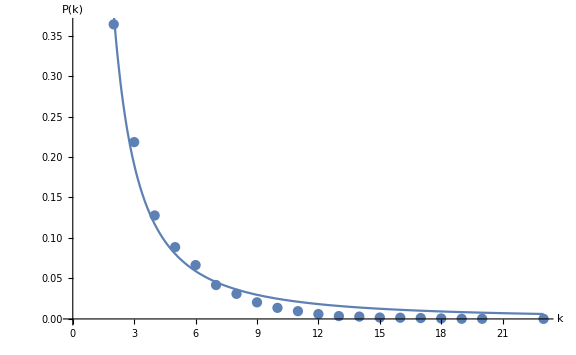
{{{1.21907,0.175006},{1.68936,0.14666}},-Graphics-}

```mathematica
m=plotModel[count,10000]
```

```mathematica
AppendTo[result,m[[1]]]
```

{{0.136652,0.964583},{{0.664569,0.123812},{1.31484,0.15496}},{{1.21907,0.175006},{1.68936,0.14666}}}